## the diving-wave ray trajectory

#### perturbation in eta

```mathematica
Clear["Global`*"]
```

```mathematica
param7={v0->2,G->0.5,p->0.25,delta->0.2,eta->0.01}
```

{v0→2,G→0.5,p→0.25,delta→0.2,eta→0.01}

```mathematica
Rl=x==(p z (2 v0+G z))/(√((1-2 (1+2 delta) eta p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2)) (√((1-(1+2 delta) (1+2 eta) p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2))+√((1-2 (1+2 delta) eta p^2 v0^2) (1-(1+2 delta) (1+2 eta) p^2 (v0+G z)^2))))/.param7/.z->-k
```

x==-(0.25088 (4-0.5 k) k)/((0.996494 √(1-0.08925 (2-0.5 k)^2)+0.801873 √(1-0.00175 (2-0.5 k)^2)) √(1-0.00175 (2-0.5 k)^2))

```mathematica
Rr=2*(√((1-(1+2 delta) (1+2 eta) p^2 v0^2)/(1+2 eta)))/((1+2 delta) G p √((1-2 (1+2 delta) eta p^2 v0^2)/(1+2 eta)))-x==(p z (2 v0+G z))/(√((1-2 (1+2 delta) eta p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2)) (√((1-(1+2 delta) (1+2 eta) p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2))+√((1-2 (1+2 delta) eta p^2 v0^2) (1-(1+2 delta) (1+2 eta) p^2 (v0+G z)^2))))/.param7/.z->-k
```

9.1965-x==-(0.25088 (4-0.5 k) k)/((0.996494 √(1-0.08925 (2-0.5 k)^2)+0.801873 √(1-0.00175 (2-0.5 k)^2)) √(1-0.00175 (2-0.5 k)^2))

```mathematica
S7=ContourPlot[x==-(0.25087962071204656 (4-0.5 k) k)/((0.9964938534682489 √(1-0.08925 (2-0.5 k)^2)+0.8018728078691783 √(1-0.0017499999999999998 (2-0.5 k)^2)) √(1-0.0017499999999999998 (2-0.5 k)^2)),{x,0,10},{k,-3.5,0},Frame->False,Axes->True,AspectRatio->Automatic,ContourStyle->{Directive[Black,Dashed,Thick]},ColorFunction->"GrayTones"];
```

```mathematica
S8=ContourPlot[9.196504955315346-x==-(0.25087962071204656 (4-0.5 k) k)/((0.9964938534682489 √(1-0.08925 (2-0.5 k)^2)+0.8018728078691783 √(1-0.0017499999999999998 (2-0.5 k)^2)) √(1-0.0017499999999999998 (2-0.5 k)^2)),{x,0,10},{k,-3.5,0},Frame->False,Axes->True,AspectRatio->Automatic,ContourStyle->{Directive[Black,Dashed,Thick]},ColorFunction->"GrayTones"];
```

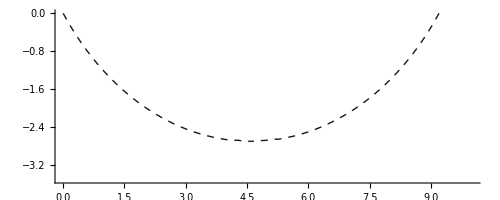

```mathematica
P7=Show[{S7,S8}]
```

```mathematica
param8={v0->2,G->0.5,p->0.25,delta->0.2,eta->0.4}
```

{v0→2,G→0.5,p→0.25,delta→0.2,eta→0.4}

```mathematica
Rl=x==(p z (2 v0+G z))/(√((1-2 (1+2 delta) eta p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2)) (√((1-(1+2 delta) (1+2 eta) p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2))+√((1-2 (1+2 delta) eta p^2 v0^2) (1-(1+2 delta) (1+2 eta) p^2 (v0+G z)^2))))/.param8/.z->-k
```

x==-(0.294628 (4-0.5 k) k)/((0.848528 √(1-0.1575 (2-0.5 k)^2)+0.608276 √(1-0.07 (2-0.5 k)^2)) √(1-0.07 (2-0.5 k)^2))

```mathematica
Rr=2*(√((1-(1+2 delta) (1+2 eta) p^2 v0^2)/(1+2 eta)))/((1+2 delta) G p √((1-2 (1+2 delta) eta p^2 v0^2)/(1+2 eta)))-x==(p z (2 v0+G z))/(√((1-2 (1+2 delta) eta p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2)) (√((1-(1+2 delta) (1+2 eta) p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2))+√((1-2 (1+2 delta) eta p^2 v0^2) (1-(1+2 delta) (1+2 eta) p^2 (v0+G z)^2))))/.param8/.z->-k
```

8.19269-x==-(0.294628 (4-0.5 k) k)/((0.848528 √(1-0.1575 (2-0.5 k)^2)+0.608276 √(1-0.07 (2-0.5 k)^2)) √(1-0.07 (2-0.5 k)^2))

```mathematica
S77=ContourPlot[x==-(0.2946278254943948 (4-0.5 k) k)/((0.848528137423857 √(1-0.1575 (2-0.5 k)^2)+0.6082762530298219 √(1-0.06999999999999999 (2-0.5 k)^2)) √(1-0.06999999999999999 (2-0.5 k)^2)),{x,0,10},{k,-3.5,0},Frame->False,Axes->True,AspectRatio->Automatic,ContourStyle->{Directive[Black,Thick]},ColorFunction->"GrayTones"];
```

```mathematica
S88=ContourPlot[8.192690730516787-x==-(0.2946278254943948 (4-0.5 k) k)/((0.848528137423857 √(1-0.1575 (2-0.5 k)^2)+0.6082762530298219 √(1-0.06999999999999999 (2-0.5 k)^2)) √(1-0.06999999999999999 (2-0.5 k)^2)),{x,0,10},{k,-3.5,0},Frame->False,Axes->True,AspectRatio->Automatic,ContourStyle->{Directive[Black,Thick]},ColorFunction->"GrayTones"];
```

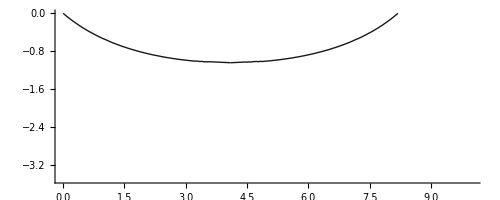

```mathematica
P8=Show[{S77,S88}]
```

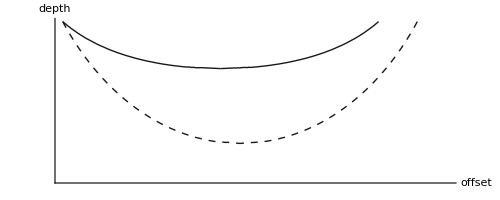

```mathematica
Show[{P7,P8},AxesLabel->{Style["offset",FontSize->20],Style["depth",FontSize->20]},Ticks->None]
```